```mathematica
vp[d_,rs_,g_]:=1/Sqrt[((1/rs-Cos[d])/(1-Cos[d]))*(1-Cos[2*g])+Sin[2*g]*Cot[d/2]]
vpp[d_,rs_,g_]:=Piecewise[{{1,((1/rs-Cos[d])/(1-Cos[d]))*(1-Cos[2*g])+Sin[2*g]*Cot[d/2]≤0}},vp[d,rs,g]]
vmin[d_,rs_,g_,h_,a_]:=Max[Min[{vpp[d,rs,g],vpp[d+2*a,rs,g],vpp[d,rs+h,g],vpp[d+2*a,rs+h,g],1}],0.01]
vmax[d_,rs_,g_,h_,a_]:=Min[{Max[{vpp[d,rs,g],vpp[d+2*a,rs,g],vpp[d,rs+h,g],vpp[d+2*a,rs+h,g],0.01}],1}]
dM[d_,rs_,g_,h_,a_,mu_]:=vmin[d,rs,g,h,a]^(-3*mu)-vmax[d,rs,g,h,a]^(-3*mu)
```

```mathematica
Manipulate[Plot[{vmin[d,rr,g,hh,aa],vmax[d,rr,g,hh,aa]},{g,0.001,Pi/2*0.9999},PlotRange->{{0,Pi/2},{0,1}}],{d,0.0001,1},{rr,1,5},{hh,0.001,0.1},{aa,0.001,0.1}]
```

```mathematica
Manipulate[Plot[{dM[d,1,g,0.01,0.005,0.4]*Sin[g]},{g,0.001,Pi/2*0.9999},PlotRange->All],{d,0.0001,2*Pi*0.9999}]
```

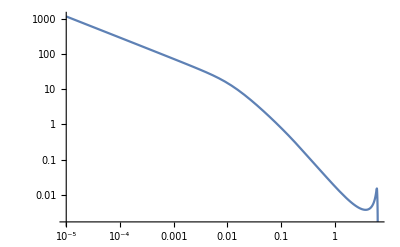

```mathematica
aa=0.005;
hh=0.01;
LogLogPlot[NIntegrate[dM[d,1,g,hh,aa,0.4]*Sin[g],{g,0.0001,Pi/2*0.9999}],{d,0.00001,2*Pi*0.9999-2*aa}]
```

NIntegrate::maxp: The integral failed to converge after 33 integrand evaluations. NIntegrate obtained 247.787 and 2.36226 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

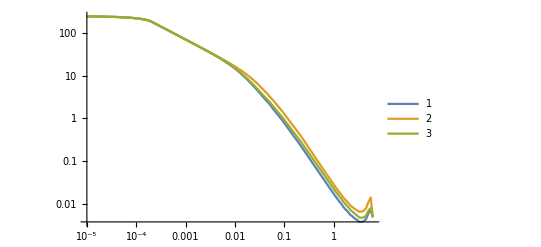

```mathematica
aa=0.005;
hh=0.01;
LogLogPlot[{NIntegrate[dM[d,1,g,hh,aa,0.4]*Sin[g],{g,0.0001,Pi/2*0.9999},MaxPoints->1,MaxRecursion->3],NIntegrate[dM[d,1,g,hh*2,aa,0.4]*Sin[g],{g,0.0001,Pi/2*0.9999},MaxPoints->1,MaxRecursion->3],NIntegrate[dM[d,1,g,hh,2*aa,0.4]*Sin[g],{g,0.0001,Pi/2*0.9999},MaxPoints->1,MaxRecursion->3]},{d,0.00001,2*Pi*0.9999-4*aa},PlotPoints->5,MaxRecursion->5,PlotLegends->Automatic]
```

```mathematica
NIntegrate[dM[0.1,1,g,hh,aa,0.4]*Sin[g],{g,0.0001,Pi/2*0.9999},MaxPoints->1,MaxRecursion->3]
```

NIntegrate::maxp: The integral failed to converge after 33 integrand evaluations. NIntegrate obtained 0.781588 and 0.0123891 for the integral and error estimates.

0.781588